```mathematica
If[!NumberQ[makePallette],NotebookEvaluate[NotebookDirectory[]~~"visualVocabDefs.nb"],NotebookEvaluate[NotebookDirectory[]~~"vvClear.nb"]];
```

## Counting by Thresholding

People have highly developed visual abilities; it is easy to look at a complicated image and to make decisions about what objects are represented in the image and how many of these objects are present. This notebook represents a first pass at counting the number of threads per centimeter in an x-ray canvas. The method adopted is somewhat primitive, but is motivated by an attempt to mimic the way that people might count. As we will see, this leads to only limited success. Other notebooks will attack the same problem from more fruitful directions.

```mathematica
TableForm[{{Hyperlink["RotateByHand",{"threadsMethodA.nb","labelRotateByHand"},BaseStyle->appColor],labelRotateByHand},{Hyperlink["HorizLines",{"threadsMethodA.nb","labelHorizLines"},BaseStyle->appColor],labelHorizLines},{Hyperlink["CountByThresh",{"threadsMethodA.nb","labelCountByThresh"},BaseStyle->appColor],labelCountByThresh},{Hyperlink["BandPassRow",{"threadsMethodA.nb","labelBandPassRow"},BaseStyle->appColor],labelBandPassRow},{Hyperlink["FilterLines",{"threadsMethodA.nb","labelFilterLines"},BaseStyle->appColor],labelFilterLines},{Hyperlink["FiltFilt",{"threadsMethodA.nb","labelFiltFilt"},BaseStyle->appColor],labelFiltFilt},{Hyperlink["VertCount",{"threadsMethodA.nb","labelVertCount"},BaseStyle->appColor],labelVertCount},{Hyperlink["Alternating",{"threadsMethodA.nb","labelAlternating"},BaseStyle->appColor],labelAlternating},{Hyperlink["FilterModel",{"threadsMethodA.nb","labelFilterModel"},BaseStyle->appColor],labelFilterModel},{Hyperlink["ManualView",{"threadsMethodA.nb","labelManualView"},BaseStyle->appColor],labelManualView}}]
```

RotateByHandthreadsMethodA.nblabelRotateByHandthreadsMethodA.nbHyperlinkHyperlinkActive | Rotate the image until the columns are vertical
HorizLinesthreadsMethodA.nblabelHorizLinesthreadsMethodA.nbHyperlinkHyperlinkActive | Looking at individual rows of the tile provides an idea of the variation in the 1D cross sections
CountByThreshthreadsMethodA.nblabelCountByThreshthreadsMethodA.nbHyperlinkHyperlinkActive | Counting the transitions by applying a threshold to the row
BandPassRowthreadsMethodA.nblabelBandPassRowthreadsMethodA.nbHyperlinkHyperlinkActive | Applying a bandpass filter to a row of the canvas x-ray
FilterLinesthreadsMethodA.nblabelFilterLinesthreadsMethodA.nbHyperlinkHyperlinkActive | Change the center frequency of the filter, apply to the row of the canvas, and count the number of threshold crossings
FiltFiltthreadsMethodA.nblabelFiltFiltthreadsMethodA.nbHyperlinkHyperlinkActive | Running the filter twice (forwards and backwards) is a common trick
VertCountthreadsMethodA.nblabelVertCountthreadsMethodA.nbHyperlinkHyperlinkActive | Counting the vertical threads using a linear filter and threshold
AlternatingthreadsMethodA.nblabelAlternatingthreadsMethodA.nbHyperlinkHyperlinkActive | The alternating model captures some characteristics of the single-line model
FilterModelthreadsMethodA.nblabelFilterModelthreadsMethodA.nbHyperlinkHyperlinkActive | Applying a bandpass filter to the output of the alternating model
ManualViewthreadsMethodA.nblabelManualViewthreadsMethodA.nbHyperlinkHyperlinkActive | Examining the 1D portrait across the thread x-ray

A special function for filter design is desFilter[ ], and checkDesign[ ] checks that the specified filter is correct. The filtering is accomplished using ListConvolve[ ] and the zero phase-shift version called filtfilt[ ].

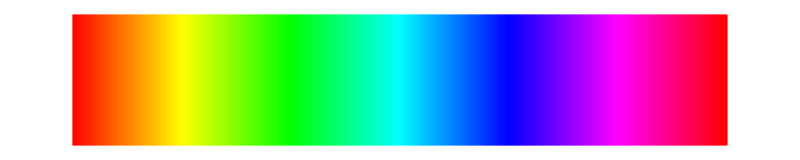

```mathematica
specLine
```

Here’s an x-ray of a small patch from F634 showing the weave pattern. Sometimes it is easier to see the patterns looking at the positive of the image.

```mathematica
Labeled[GraphicsRow[{allImagesXray[[f634Tile]],ColorNegate[allImagesXray[[f634Tile]]]},ImageSize->600],"An x-ray negative and its inversion",LabelStyle->captionStyle]
```

-Graphics-An x-ray negative and its inversion

To make things a little easier at first, it is possible to straighten out the image by rotating it. Notice the black trim (padding) around the sides. For now, choose the amount of rotation by eye. A value of about 0.026 radians makes the threads reasonably vertical and horizontal. Set the value numerically by clicking the small + box and entering the desired value.

```mathematica
labelRotateByHand="Rotate the image until the columns are vertical (set to 0.026 radians)";
infoRotateByHand="Choose the amount of rotation by eye. A value of about 0.026 radians makes the threads reasonably vertical and horizontal.\n\nUse the slider or set the value numerically by clicking the small + box and entering the desired value.";
Manipulate[Image[ImageRotate[ColorNegate[allImagesXray[[f634Tile]]],θ],ImageSize->400],Row[{Control[{{θ,0.0,"rotation angle θ (radians)"},-Pi/8,Pi/8,Appearance->"Labeled"}],Spacer[20],info[infoRotateByHand]}],FrameLabel->Style[labelRotateByHand,Medium],TrackedSymbols->{θ},SaveDefinitions->True]
```

Notice that the size of the image has increased slightly to accomodate the added black trim (padding).

```mathematica
{originalColumnSize,originalRowSize}=ImageDimensions[allImagesXray[[f634Tile]]];
{newColumnSize,newRowSize}=ImageDimensions[ImageRotate[ColorNegate[allImagesXray[[f634Tile]]],0.026]];
{originalColumnSize,originalRowSize,newColumnSize,newRowSize}
```

{473,473,486,486}

```mathematica
specLine
```

-Graphics-

Consider counting along a horizontal line... which line shall we pick? With the row specified by the green line, the plot on the right shows the pixel values (normalized to lie between 0 and 1) across the image in that row. Imagine using this row of values to try and count the threads. Using the rectangle model (or the functional model) and picking a nice row, a simple threshold will cut across each of the peaks (both narrow and fat) twice (once up and once down) and so will nicely count the threads. But if we look at the real x-ray tile (this is F634, which is not one of the more difficult canvases), it’s not going to be easy. We could try to pick a good row, where as many transitions as possible are cleanly visible. But while we probably have a pretty good intuitive idea of what a row that is easy-to-count by hand might look like (one with easy-to-see features), it is not clear how to choose such a row automatically. And there are a lot of rows to choose from.

```mathematica
labelHorizLines="Looking at individual rows of the tile provides an idea of the variation in the 1D cross sections";
infoHorizLines="With the row specified by the green line, the plot on the right shows the pixel values, reducing the problem to a 1D function.\n\nImagine using this row of values to try and count the threads. With the simple models, this will probably work as long as we can choose the row well.\n\nFor example, consider row 383 of the rectangle model. A threshold at 0.6 will catch each crossing from low to high and from high to low.\n\nBut if we pick the row poorly (e.g. row 368 for the rectangle model), the count will be only half as large.\n\nFor real x-rays, it's even trickier! Look at rows 380 to 385 of the x-ray tile. These are fairly good, but even here a simple threshold may not count every crossing of every thread.";
Manipulate[Module[{img,col,row},
If[invert=="negative",img=allIm[[i]],img=ColorNegate[allIm[[i]]]];
{col,row}=ImageDimensions[img];
tLine=threadLine[img,row-thisRow+1];
Row[{Show[Image[img,ImageSize->350],Graphics[{Green,Opacity[0.4],Thickness[0.02],Line[{{0,thisRow},{col,thisRow}}]}]],Spacer[20],ListLinePlot[tLine,PlotRange->{{1,col},{0,1}},ImageSize->250]}]],Row[{Control[{{i,1,"image"},Thread[Range[Length[allIm]]->allImNames],ControlType->PopupMenu}],Spacer[20],Control[{{invert,"negative",""},{"negative","positive"}}]}],Row[{Control[{{thisRow,383,"row number"},1,470,1,Appearance->"Labeled"}],Spacer[40],info[infoHorizLines]}],FrameLabel->Style[labelHorizLines,Medium],TrackedSymbols->{thisRow,i,invert},SaveDefinitions->saveDef]
```

For the sake of concreteness, choose row 383 (of the rectangle model). By eye, we would be counting the number of transitions from white to black and back to white again; in terms of the numbers, we might try and count how may times the signal goes from high to low and then back from low to high.

```mathematica
specLine
```

-Graphics-

First let's be naive and pick a threshold value τ and simply count how many times the line crosses this transition value. The threshold is given by a value τ and the 1-D thread values are inherited from the above figure. One way to count the transitions is implemented in the following function upCross[]. This subtracts the threshold value from the signal, and then takes the Sign[ ] of each element. Taking the Difference[] gives a vector that contains lots of zeros, a +2 whenever the signal crosses from below the threshold to above and a -2 whenever it crosses from above the threshold to below. Count[ ] counts how many +2s there are, and this is the output of the upCross[ ] function.

```mathematica
upCross[x_,τ_]:=Count[Differences[Sign[x-τ]],2];
```

This function can be visualized as in the following interactive example: the green line represents the threshold value. The values of the thread line are shown in blue. The right hand plot shows the Sign[ ] function which is used to carry out the counting using the upCross[ ] function. The output of upCross[ ] is printed to the right. For the default values this is 22. As the threshold changes (to extreme values), the number of crossings change.

```mathematica
labelCountByThresh="Counting the transitions by applying a threshold to the row";
introCountByThresh="The function upCross[] counts how may times the signal crosses the threshold from low to high.\n\nThe green line represents the threshold value and the values of the thread line are shown in blue. The right hand plot shows the Sign[] function used inside upCross[ ]. The numerical output of upCross[ ] (the number of upcrossings) is displayed to the right.\n\nFor row 383 of the rectangle model, this is 22, and the value remains fixed over a large threshold range (form about 0.4 to 0.8).\n\nBut for the x-ray tile, as the threshold changes, the number of crossings change. Look at row 383; the count varies between 23 and 27 (or so).";
Manipulate[Module[{col,row,img},img=allIm[[i]];
{col,row}=ImageDimensions[img];
tLine=threadLine[img,row-thisRow+1];Row[{Show[ListLinePlot[tLine,ImageSize->300],Graphics[{Darker[Green],Thickness[0.01],Line[{{1,τ},{Length[tLine],τ}}]}]],Spacer[20],ListLinePlot[Sign[tLine-τ],ImageSize->300,PlotRange->{-1.2,1.2}],Spacer[20],upCross[tLine,τ]}]],Row[{Control[{{i,2,"image"},Thread[Range[Length[allIm]]->allImNames],ControlType->PopupMenu}],Spacer[20],Control[{{thisRow,383,"row number"},1,470,1,Appearance->"Labeled"}]}],Row[{Control[{{τ,0.7,"threshold τ"},0,1,Appearance->"Labeled"}],Spacer[20],info[introCountByThresh]}],
FrameLabel->Style[labelCountByThresh,Medium],TrackedSymbols->{τ,thisRow,i},SaveDefinitions->True]
```

HW: For the rectangle mode, pick a threshold. Use the animation feature to scan through the various rows. Can you pick a value that will give the same answer for every row?

```mathematica
specLine
```

-Graphics-

It should be clear (particularly for the x-ray tile), that it is very difficult to pick a threshold that gives the right count, even after picking an apparently easy-to-count row of the x-ray image. What is needed is a way to smooth out the fluctuations, to decrease the sensitivity to small changes in the threshold value. One way to proceed is to use a linear filter. With proper design, a bandpass filter can accomplish two things: it can remove the DC constant offset and remove high frequency jiggles that plague the operation.

How can we specify the BPF? The total length of the signal in the x-ray tile is Length[threadLine]=486. Eyeballing the thread count, it is clear that there are between 20 and 27 threads across the path of the light green line. Hence the pass band of the filter can be centered around normalized frequency 0.5 (23/486) π, or 0.075 and the bandwidth needs to cover the range from 20 to 27 (which is the range we might hope to count over). Thus a rough specification for the filter is that it should be

```mathematica
{0.5 (20/486) π,0.5 (23/486) π,0.5 (27/486) π}
```

{0.0646418,0.0743381,0.0872665}

Thus a rough specification for the filter is that it should be unity between 0.06 and 0.08 and zero outside this range.

Here’s a candidate filter, designed using the designFIR[ ] function. The specification of the magnitude response of the filter is given by the red curve (this is defined directly by the points in filterSpec) and the blue gives the actual filter as designed by the function designFIR[ ]. The plots are made by the checkDesign[ ] function. It is always a good idea to check the design to make sure nothing bad has happened.

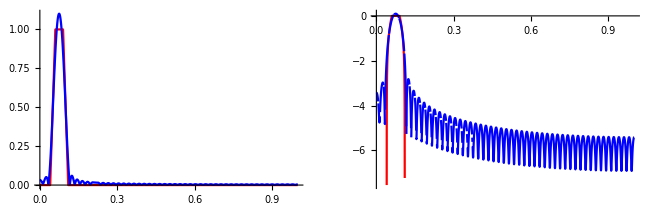
-Graphics-Design and implementation of a bandpass filter

```mathematica
filterSpec={{0,0},{0.04,0.0},{0.06,1},{0.09,1},{0.11,0}{1,0}};
desFilter=designFIR[filterSpec,101];
Labeled[GraphicsRow[{checkDesign[filterSpec,desFilter,300,"Linear"],checkDesign[filterSpec,desFilter,300,"Log"]}],"Design and implementation of a bandpass filter",LabelStyle->captionStyle]
```

```mathematica
labelBandPassRow="Applying a bandpass filter to a row of the canvas x-ray";
infoBandPassRow="The bandpass filter is applied to any row of the image.\n\nFor the synthetic models, the results are good (for instance, look at row 364 for the rectangle model or row 383 for the functional model).\n\nThe x-ray tile is more tricky and still varies considerably by row.\n\nOne advantage is that it's no longer necessary to pick a threshold: because of the filtering, the 1D signal is centered on zero.";
Manipulate[Module[{col,row,img},img=allIm[[i]];
{col,row}=ImageDimensions[img];
tLine=threadLine[img,row-thisRow+1];
filteredThread=ListConvolve[desFilter,tLine,{1,1},0];GraphicsRow[{ListLinePlot[tLine,ImageSize->300],ListLinePlot[filteredThread,ImageSize->300]}]],Row[{Control[{{i,2,"image"},Thread[Range[Length[allIm]]->allImNames],ControlType->PopupMenu}],Spacer[20],Control[{{thisRow,383,"row number"},1,470,1,Appearance->"Labeled"}],Spacer[20],info[infoBandPassRow]}],FrameLabel->Style[labelBandPassRow,Medium],TrackedSymbols->{thisRow,i},SaveDefinitions->True]
```

```mathematica
specLine
```

-Graphics-

That’s an improvement, but maybe there are better filters. This demonstration allows specification of both the center frequency and the bandwidth (the range of frequencies that will be passed by the filter).

```mathematica
labelFilterLines="Change the center frequency of the filter and the bandwidth, apply to the row of the canvas, and count the number of threshold crossings";
infoFilterLines="The left shows the frequency response of a filter with center frequency specified by the slider.\n\nThe right hand plot shows a filtering of row 383 (of the x-ray thread tile).\n\nWhen the center frequency is set too low, the filtered signal has too few unndulations.\n\nWhen the center frequency is set too high, the filtered signal has too many undulations.\n\nBetween too low and too high are some sweet spots that hit the correct answer (in this case 23).";
Manipulate[filterSpec={{0,0},{Max[centerF-bw-0.01,0.01],0},{Max[centerF-bw,0.02],1},{centerF+bw,1},{centerF+bw+0.01,0},{1,0}};
desFilter=designFIR[filterSpec,101];
filteredThread=ListConvolve[desFilter,threadLine[allIm[[1]],90],{1,1},0];
Row[{checkDesign[filterSpec,desFilter,300,"Linear"],Spacer[20],
ListLinePlot[filteredThread,ImageSize->300], Spacer[20],upCross[filteredThread,0]}],Control[{{centerF,0.09,"normalized center frequency"},0.04,0.3,Appearance->"Labeled"}],
Row[{Control[{{bw,0.02,"normalized bandwidth"},0.001,0.6,Appearance->"Labeled"}],Spacer[20],info[infoFilterLines]}],
FrameLabel->Style[labelFilterLines,Medium],TrackedSymbols->{centerF,bw},SaveDefinitions->True]
```

Observe that with a center frequency of about 0.09 and bandwidth about 0.02 (the defaults) this shows 22 upcrossings. Moreover, this value is not overly sensitive to the particular center frequency: 23 is still the count over a range from about 0.08 to 0.11. Other values of the count remain unchanged only over smaller intervals. The outputs tend to be small at the beginning, which occurs because the initialization of the filter is at all zero values.

```mathematica
specLine
```

-Graphics-

A common trick to fix this is to run the filter twice: once forwards and once backwards. Adding the two outputs together gives better behavior at the endpoints. This is implemented in the filtfilt[ ] function, which replaces the built in function ListConvolve[]. In this particular case, using filtfilt[ ] doesn't change the results much, but in some situations it may be helpful.

```mathematica
labelFiltFilt="Running the filter twice (forwards and backwards) is a common trick";
infoFiltFilt="This is the same setup as the previous example, but the filter is exectuted twice: once forwards and once backwards.\n\nThis common trick tends to reduce end effects (the slow startup of the filter).\n\nThe correct answer (24) is found over a somewhat larger range of center frequencies and bandwidths. The left and right edges do not die away towards zero as in the previous (unidirectional filtering) case.";
Manipulate[filterSpec={{0,0},{Max[centerF-bw-0.01,0.01],0},{Max[centerF-bw,0.02],1},{centerF+bw,1},{centerF+bw+0.01,0},{1,0}};
desFilter=designFIR[filterSpec,101];
filteredThread=filtfilt[desFilter,threadLine[allIm[[1]],90]];
Row[{checkDesign[filterSpec,desFilter,300,"Linear"],Spacer[20],ListLinePlot[filteredThread,ImageSize->300],Spacer[20],upCross[filteredThread,0]}],
Control[{{centerF,0.09,"normalized center frequency"},0.03,0.3,Appearance->"Labeled"}],
Row[{Control[{{bw,0.02,"normalized bandwidth"},0.001,0.6,Appearance->"Labeled"}],Spacer[20],info[infoFiltFilt]}],FrameLabel->Style[labelFiltFilt,Medium],TrackedSymbols->{centerF,bw},SaveDefinitions->True]
```

```mathematica
specLine
```

-Graphics-

Of course, we could do the same thing for vertical lines. Again, which column shall we pick and what center frequency should we choose?

```mathematica
labelVertCount="Counting the vertical threads using a linear filter and threshold";
infoVertCount="Cghoose a column of the image, which is indicated by the green line.\n\nThe values of the pixels in the image are shown on the right as a 1D function.\n\nSelect a center frequency for the filter. The filter specification (red) and the implemented filter (blue) are superimposed on the bottom left.\n\nThe result of applying this filter to the column (using the forwards-backwards trick) is plotted on the bottom right.\n\nTry picking a good looking column and count it by hand. How accurate is the automated count in the bottom right?";
Manipulate[{col,row}=ImageDimensions[allIm[[1]]];
threadLineV=ImageData[allIm[[1]]][[1;;row,column]];
filterSpec={{0,0},{Max[centerF-bw-0.01,0.01],0},{Max[centerF-bw,0.02],1},{centerF+bw,1},{centerF+bw+0.01,0},{1,0}};desFilter=designFIR[filterSpec,101];
filteredThread=filtfilt[desFilter,threadLineV];
Column[{Row[{Show[Image[allIm[[1]],ImageSize->300],Graphics[{Green,Opacity[0.4],Thickness[0.02],Line[{{column,0},{column,row}}]}]],Spacer[20],ListLinePlot[threadLineV,PlotRange->{{1,row},{0,1}},ImageSize->250]}],
Row[{checkDesign[filterSpec,desFilter,300,"Linear"],Spacer[20],ListLinePlot[filteredThread,ImageSize->300],Spacer[20],upCross[filteredThread,0]}]}],
{{column,243},1,486,1,Appearance->"Labeled"},Control[{{centerF,0.09,"normalized center frequency"},0.03,0.3,Appearance->"Labeled"}],Row[{Control[{{bw,0.02,"normalized bandwidth"},0.001,0.6,Appearance->"Labeled"}],Spacer[20],info[infoVertCount]}],FrameLabel->Style[labelVertCount,Medium],TrackedSymbols->{column,centerF,bw},SaveDefinitions->True]
```

```mathematica
specLine
```

-Graphics-

The approach of this notebook is to pick a horizontal (or vertical) line and to extract the 1D signal along this line. Then a linear filter is followed by a threshold to count how many times the signal crosses the threshold. What kind of assumptions does this imply that we are making about the weave pattern that we are trying to detect? Consider the alternating model (which is repeated below). This model supposes that the signal is the sum of an offset and a collection of spikes that are shaped (something like) a sine wave, perhaps with some nonlinear distortion. Since the peaks are not always of the same height, these may also vary in a simple structured way using the amp parameter. With no noise (the default), these are too sterile, too regular. The noise slider adds noise to make them a bit more realistic. The slope slider adds a trend with slope to the data, which can be interpreted as a slow change from light to dark (or from dark to light) over the extent of the image.

```mathematica
labelAlternating="The alternating model captures some characteristics of the single-line model";
infoAlternating="In the alternating model, parameters a and b control the widths of two alternating peaks. The amp parameter controls the relative size of the peaks. The noise parameter adds noise. The slope parameter adds a trend.\n\nPlacing a threshold at 0.6, observe that as the amp slider changes the sizes of adjacent peaks, it also changes a count of the crossings. When the peaks are all roughly the same size, the count should be 20, when the amp slider is turned down, the count is 10.\n\nThe slope can also influence (change) the count (explain why).\n\nIf there is a significant amount of noise, a threshold will become an ineffective method of counting since there will be multiple small crossings.";
altFun[x_,a_,b_,amp_]:=Piecewise[{{altFun[x-(a+b),a,b,amp],x>a+b},{Sin[2 Pi/a x],0<x<a},{amp Sin[2 Pi/b (x-a)],a<x<a+b},{altFun[x+(a+b),a,b,amp],x<0}}];
Manipulate[altSamp=Table[slope (x-1/2)+0.5 Clip[altFun[x,a,b,amp],{0,1.2}]+RandomVariate[NormalDistribution[0.3,σ]],{x,0,1,1/500}];
Show[ListLinePlot[altSamp,PlotRange->{0,1},ImageSize->350],Graphics[{Darker[Green],Thickness[0.01],Line[{{1,τ},{Length[tLine],τ}}]}]],
{{a,0.02},0,0.2,Appearance->"Labeled"},{{b,0.08},0,0.2,Appearance->"Labeled"},{{amp,1},0,1.2},{{slope,0,"slope"},-0.4,0.4},{{σ,0.001,"noise"},0.001,0.16},Row[{Control[{{τ,0.54,"threshold τ"},0,1,Appearance->"Labeled"}],Spacer[20],info[infoAlternating]}],FrameLabel->Style[labelAlternating,Medium],TrackedSymbols->{a,b,amp,σ,slope,τ},SaveDefinitions->True]
```

```mathematica
specLine
```

-Graphics-

In the noise-free, trend-free case, each of these can be counted perfectly using the threshold method. However, if there is a significant amount of noise, a single threshold will become ineffective since there will be multiple small crossings of any given threshold. Similarly, if the trend is nonzero, the threshold becomes ineffective because of the tilt of the curve. In fact, these two potential problems show why the bandpass filtering is so useful in this problem; it ameliorates both the trend problem and the noise problem. The effect of the filtering on the output of the models above for filters with a variety of center frequencies is shown in the next figure. The bandpass filter rejects the bulk of the slope (by flattening out the trend) and removes the bulk of the noise by attenuating the high frequency jitter. Observe that both models A and B act roughly the same under the effect of the filtering. This is a good example of the interplay between preprocessing and the choice of algorithm.

In terms of the visual vocabulary, a high pass (sharpening) filter should remove the slow trend. A low pass (blur) filter should work to ameliorate the noise. The bandpass filter is a concatenation of both the high and the lowpass filters.

```mathematica
labelFilterModel="Applying a bandpass filter to the output of the alternating model";
infoFilterModel="With the default a (0.02) and b (0.08) the correct count is 20.\n\nUsing the bandpass filter, the count of zero crossings is reasonably robust to height changes, slope changes, and noise.";
Manipulate[filterSpec={{0,0},{centerF-0.02,0},{centerF-0.01,1},{centerF+0.01,1},{centerF+0.02,0},{1,0}};
desFilter=designFIR[filterSpec,101];
filteredThread=filtfilt[desFilter,altSamp];
altSamp=Table[slope (x-1/2)+0.5 Clip[altFun[x,a,b,amp],{0,1.2}]+RandomVariate[NormalDistribution[0.3,σ]],{x,0,1,1/500}];
GraphicsGrid[{{ListLinePlot[altSamp,ImageSize->300],checkDesign[filterSpec,desFilter,300,"Linear"]},{ListLinePlot[filteredThread,ImageSize->300,PlotRange->{-0.3,0.3}],Style[upCross[filteredThread,0],Large]}}],Row[{Control[{{a,0.02},0,0.2,Appearance->"Labeled"}],Spacer[20],Control[{{b,0.08},0,0.2,Appearance->"Labeled"}]}],Row[{Control[{{amp,1},0,1.2}],Spacer[20],Control[{{slope,0,"slope"},-0.4,0.4}]}],
Row[{Control[{{σ,0.001,"noise"},0.001,0.16}],Spacer[20],Control[{{centerF,0.08,"center frequency"},0.03,0.3,Appearance->"Labeled"}],Spacer[20],info[infoFilterModel]}],FrameLabel->Style[labelFilterModel,Medium],TrackedSymbols->{a,b,amp,σ,slope,centerF},SaveDefinitions->True]
```

HW: Add the ability of the filter to specify the bandwidth as well as the center frequency.

```mathematica
specLine
```

-Graphics-

There are other ways that the threshold counting method can fail that cannot be fixed with a bandpass filter. 
(1) There could be a drop-out in the signal, a region where the x-ray does not show any significant up or down undulation (HW: find a image with a bad region and try to apply).
(2) We picked the row or column over which to analyze the signal by eye, with the intent of picking a good row. If this were to be applied as an automated method, there is no guarantee that the algorithm would pick a good place to do the count. (HW: pick a bad row and see if it’s still possible to find the correct answer) 
(3) We manually rotated the image -- can this be done automatically, and what goes wrong if the rotation is incorrect? (HW: try doing the above counting by thresholding procedure on the unrotated image, or on an incorrectly rotated image). 

More generally, consider counting across any single line. There are three problems with this, two technical and one conceptual. The technical problems can probably be solved, but the conceptual problem requires a revision of the basic strategy of “counting along a line”. First the easy problems:
(1) The line may not be aligned with the underlying weave pattern -- to fix this would require a way to automatically rotate the image so make it horizontal or vertical. Indeed this is feasible and can be done using a kind of projection and summation that is closely related to the Radon Transform.
(2) When doing any kind of counting, there is always the possibility of missing an item or of encountering an extra item. While the human can be counted on to make reasonable judgment calls, computer programs are not as flexible.
The conceptual problem is this: counting on a line is fundamentally a one-dimensional activity, yet the “real” problem is fundamentally a two-dimensional activity. The horizontal count and the vertical count are not really independent, since crossings of one are revealed by looking at areas of the weave. For example, when counting by eye, there may be a dropout in the weave across the line we are looking at. Nonetheless, we can easily scan up and down at that point and realize that indeed there must be a thread crossing where looking at the single thread there would appear to be none. So it would clearly be an improvement to be able to use (at least) local information around the thread on which we are centering the counting procedure.

HW: use small 2D patches of an image along with a (2-D) bandpass filter and a thresholding operation to find intersections and do vertical and horizontal thread counts simultaneously. Can this be made to work reliably? Try it first on a simple 2D model (where it will work) and then on a real thread x-ray image (where it will most likely not work). What are the sources of error?

HW: Observe that the horizontal and vertical threads are not orthogonal to each other in all cases. Make a simple 2D sinusoidal model. In such a case, estimate the difference between (a) counting along the thread and (b) counting along an orthogonal line to the thread. Your answer should estimate the error as a function of the angle between the threads and the orthogonal. Whether counting horizontal threads or vertical threads, the skew (nonorthogonality) gives one source of error while the rotation of the image gives another source of error.  If either the rotation or the skew are too large, then the 1D method will give erroneous results (at best) or fail dramatically (at worst).

```mathematica
specLine
```

-Graphics-

```mathematica
labelManualView="Examining the 1D portrait across the thread x-ray";
infoManualView="There is no reason that the 1D function needs to be drawn from a single row or column of an image. The function could be taken from any desired line or curve.\n\nMove the endpoints of the green line with the mouse, and observe the resulting 1D function.\n\nWhich of the tiles looks easiest to count, and which looks the most difficult?";
slope[st_,en_]:=Module[{a,b,mat},mat={{st[[1]],1},{en[[1]],1}};
If[Abs[Det[mat]]>0.0001,{a,b}=Inverse[mat].{st[[2]],en[[2]]};];
a];vh=0;
{col,row}=ImageDimensions[allImagesXray[[f634Tile]]];
Manipulate[Module[{img,start,end,s,vh,xVals,yVals},
If[invert=="negative",img=allImagesXray[[i]],img=ColorNegate[allImagesXray[[i]]]];
{start,end}=pt;s=slope[start,end];
If[Abs[s]<1,vh=0,vh=1];
Row[{Show[Image[img,ImageSize->350],Graphics[{Green,Thickness[0.01],Line[{start,end}]}]],If[vh==0,xVals=Interpolation[{start,end},InterpolationOrder->1];xyVals=Table[{x,N[xVals[x]]},{x,Min[start[[1]],end[[1]]],Max[start[[1]],end[[1]]]}];,yVals=Interpolation[{Reverse[start],Reverse[end]},InterpolationOrder->1];xyVals=Table[Reverse[{y,N[yVals[y]]}],{y,Min[start[[2]],end[[2]]],Max[start[[2]],end[[2]]]}];];Spacer[20],ListLinePlot[ImageValue[img,xyVals],ImageSize->250,PlotRange->{0,1}]}]],Row[{Control[{{i,f634Tile,"image"},Thread[Range[numFilesX]->imageNamesX],ControlType->PopupMenu}],Spacer[20],Control[{{invert,"negative",""},{"negative","positive"}}],Control[{{pt,{{col/5,row/2},{4 col/5,row/2}}},Locator}],Spacer[20],info[infoManualView]}],FrameLabel->Style[labelManualView,Medium],TrackedSymbols->{pt,i,invert},SaveDefinitions->saveDef]
```

HW: Apply a linear filter (with adjustable center frequency and bandwidth) to the above demonstration.

HW: Apply the Radon transform to automatically identify the rotation of the canvas, then attempt the threshold count.

HW: Apply adaptive thresholding as a method of preprocessing and then attempt to count the threads using a threshold. For which image tiles does this make the counting easier? Does it make any of them more difficult to count?